```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
Leads=Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{1},299,{{0.461335-0.0000344515 ⅈ,0.191132-0.0000279943 ⅈ,0.112061-0.0000304181 ⅈ,8,0.0964055-0.0000346394 ⅈ,0.117282-0.0000339417 ⅈ,0.192872-0.0000292268 ⅈ},{1},10,{1},{1}}}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Leads[[ω*100+1]]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SL[ω,δ,t,ϵ,m]=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
pris=ParallelTable[{ω,tr[ω,0.0001,1,0,7]},{ω,Range[0,3,0.01]}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999997},{0.27,0.999999},{0.28,0.999999},{0.29,1.},{0.3,1.},{0.31,1.},{0.32,1.},{0.33,1.},{0.34,1.},{0.35,1.},{0.36,1.},{0.37,1.},{0.38,1.},{0.39,1.},{0.4,1.00001},{0.41,1.00014},{0.42,1.99993},{0.43,1.99999},{0.44,2.},{0.45,2.},{0.46,2.},{0.47,2.},{0.48,2.},{0.49,2.},{0.5,2.},{0.51,2.},{0.52,2.},{0.53,2.},{0.54,2.},{0.55,2.},{0.56,2.},{0.57,2.},{0.58,2.},{0.59,2.},{0.6,2.},{0.61,2.},{0.62,2.},{0.63,2.},{0.64,2.},{0.65,2.},{0.66,2.},{0.67,2.},{0.68,2.},{0.69,2.},{0.7,2.},{0.71,2.},{0.72,2.},{0.73,2.},{0.74,2.},{0.75,2.},{0.76,2.},{0.77,2.},{0.78,2.},{0.79,2.},{0.8,2.},{0.81,2.},{0.82,2.},{0.83,2.00001},{0.84,2.00004},{0.85,2.9995},{0.86,2.99998},{0.87,2.99999},{0.88,3.},{0.89,3.},{0.9,3.},{0.91,3.},{0.92,3.},{0.93,3.},{0.94,3.},{0.95,3.},{0.96,3.},{0.97,3.},{0.98,3.},{0.99,3.},{1.,3.},{1.01,3.},{1.02,3.},{1.03,3.},{1.04,3.},{1.05,3.},{1.06,3.},{1.07,3.},{1.08,3.},{1.09,3.},{1.1,3.},{1.11,3.},{1.12,3.},{1.13,3.},{1.14,3.},{1.15,3.},{1.16,3.},{1.17,3.},{1.18,3.},{1.19,3.},{1.2,3.},{1.21,3.},{1.22,3.},{1.23,3.},{1.24,3.},{1.25,3.},{1.26,3.},{1.27,3.},{1.28,3.},{1.29,3.},{1.3,3.},{1.31,3.},{1.32,3.},{1.33,3.},{1.34,3.},{1.35,3.},{1.36,3.},{1.37,3.},{1.38,3.},{1.39,3.},{1.4,3.},{1.41,3.},{1.42,3.},{1.43,3.},{1.44,3.},{1.45,3.},{1.46,3.},{1.47,3.},{1.48,3.},{1.49,3.},{1.5,3.},{1.51,3.},{1.52,3.},{1.53,3.},{1.54,3.},{1.55,3.},{1.56,3.},{1.57,3.},{1.58,3.},{1.59,3.},{1.6,3.},{1.61,3.},{1.62,3.},{1.63,3.},{1.64,3.},{1.65,3.},{1.66,3.},{1.67,3.},{1.68,3.},{1.69,3.},{1.7,3.},{1.71,3.},{1.72,3.},{1.73,3.},{1.74,3.},{1.75,2.99999},{1.76,2.99991},{1.77,2.00012},{1.78,2.00001},{1.79,2.},{1.8,2.},{1.81,2.},{1.82,2.},{1.83,2.},{1.84,2.},{1.85,2.},{1.86,2.},{1.87,2.},{1.88,2.},{1.89,2.},{1.9,2.},{1.91,2.},{1.92,2.},{1.93,2.},{1.94,2.},{1.95,2.},{1.96,2.},{1.97,2.},{1.98,2.},{1.99,2.},{2.,2.},{2.01,2.},{2.02,2.},{2.03,2.},{2.04,2.},{2.05,2.},{2.06,2.},{2.07,2.},{2.08,2.},{2.09,2.},{2.1,2.},{2.11,2.},{2.12,2.},{2.13,2.},{2.14,2.},{2.15,2.},{2.16,2.},{2.17,2.},{2.18,2.},{2.19,2.},{2.2,2.},{2.21,2.},{2.22,2.},{2.23,2.},{2.24,2.},{2.25,2.},{2.26,2.},{2.27,2.},{2.28,2.},{2.29,2.},{2.3,2.},{2.31,2.},{2.32,2.},{2.33,2.},{2.34,2.},{2.35,2.},{2.36,2.},{2.37,2.},{2.38,2.},{2.39,2.},{2.4,1.99999},{2.41,1.99986},{2.42,1.00007},{2.43,1.00001},{2.44,1.},{2.45,1.},{2.46,1.},{2.47,1.},{2.48,1.},{2.49,1.},{2.5,1.},{2.51,1.},{2.52,1.},{2.53,1.},{2.54,1.},{2.55,1.},{2.56,1.},{2.57,1.},{2.58,1.},{2.59,1.},{2.6,1.},{2.61,1.},{2.62,1.},{2.63,1.},{2.64,1.},{2.65,1.},{2.66,1.},{2.67,1.},{2.68,1.},{2.69,1.},{2.7,1.},{2.71,1.},{2.72,1.},{2.73,1.},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

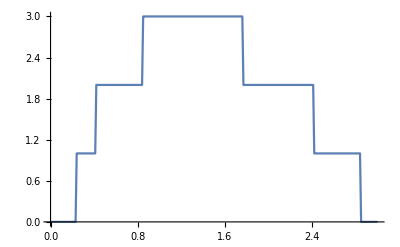

```mathematica
ListPlot[pris[[2]],Joined->True]
```

```mathematica
RandomSample[Join[Flatten[Table[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10},5]],Flatten[Table[{imp11,imp12,imp13,imp14},6]],Flatten[Table[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8},0]],Table[imp,26]]]
```

{imp4,imp3,imp1,imp13,imp,imp,imp,imp14,imp2,imp4,imp,imp14,imp,imp,imp,imp5,imp2,imp13,imp13,imp,imp10,imp,imp13,imp12,imp9,imp3,imp,imp2,imp7,imp6,imp6,imp12,imp14,imp6,imp7,imp,imp1,imp,imp,imp8,imp12,imp4,imp11,imp10,imp6,imp,imp,imp1,imp4,imp5,imp14,imp2,imp,imp2,imp8,imp,imp11,imp12,imp,imp3,imp9,imp,imp11,imp8,imp8,imp3,imp11,imp5,imp6,imp9,imp1,imp11,imp5,imp9,imp5,imp,imp1,imp7,imp7,imp10,imp,imp10,imp13,imp13,imp7,imp10,imp4,imp,imp14,imp3,imp12,imp,imp9,imp14,imp,imp12,imp11,imp8,imp,imp}

```mathematica
Dimensions[%87]
```

{96}

```mathematica
Clear[imp12,imp1,imp7,imp13,imp8,imp8,imp,imp,imp,imp,imp5,imp12,imp,imp13,imp6,imp4,imp2,imp9,imp10,imp,imp6,imp4,imp10,imp8,imp11,imp10,imp14,imp1,imp,imp3,imp,imp1,imp,imp3,imp13,imp14,imp1,imp5,imp,imp12,imp2,imp7,imp14,imp11,imp8,imp11,imp,imp,imp,imp1,imp2,imp8,imp,imp10,imp10,imp9,imp2,imp12,imp,imp11,imp7,imp6,imp4,imp,imp13,imp12,imp11,imp,imp6,imp,imp13,imp4,imp5,imp9,imp7,imp,imp12,imp5,imp,imp9,imp11,imp,imp,imp4,imp6,imp3,imp,imp7,imp,imp14,imp13,imp5,imp,imp14,imp9,imp2,imp3,imp,imp3,imp14]
```

```mathematica
l1={{2,12,14},{4,10,12},{6,10,8},{2,4,12},{4,6,10}}
```

{{2,12,14},{4,10,12},{6,10,8},{2,4,12},{4,6,10}}

```mathematica
l={{1,3,13},{3,13,11},{3,5,13},{5,7,9},{11,9,5}}
```

{{1,3,13},{3,13,11},{3,5,13},{5,7,9},{11,9,5}}

```mathematica
x=RandomSample[Flatten[RandomSample[l,1]],2]
```

{13,3}

```mathematica
x[[2]]
```

3

```mathematica
Clear[m]
```

```mathematica
μ1=RandomInteger[{1,14}]; μ2=RandomInteger[{1,14}];μ3=RandomInteger[{1,14}]; μ4=RandomInteger[{1,14}];μ5=RandomInteger[{1,14}]; μ6=RandomInteger[{1,14}]; μ7=RandomInteger[{1,14}];μ8=RandomInteger[{1,14}];μ9=RandomInteger[{1,14}]; μ10=RandomInteger[{1,14}]; μ11=RandomInteger[{1,14}];μ12=RandomInteger[{1,14}];μ13=RandomInteger[{1,14}]; μ14=RandomInteger[{1,14}]
```

13

```mathematica
m[ω_,ϵ1_]:=Block[{Tin=T1[1,7],T=ρ[1,7]},
imp1:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];imp9:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{μ14,μ14}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];tra1:=Block[{J=SL[ω,0.0001,1,0,7]},
b=Block[{},
lista={{imp4,imp3,imp1,imp13,imp,imp,imp,imp14,imp2,imp4,imp,imp14,imp,imp,imp,imp5,imp2,imp13,imp13,imp,imp10,imp,imp13,imp12,imp9,imp3,imp,imp2,imp7,imp6,imp6,imp12,imp14,imp6,imp7,imp,imp1,imp,imp,imp8,imp12,imp4,imp11,imp10,imp6,imp,imp,imp1,imp4,imp5,imp14,imp2,imp,imp2,imp8,imp,imp11,imp12,imp,imp3,imp9,imp,imp11,imp8,imp8,imp3,imp11,imp5,imp6,imp9,imp1,imp11,imp5,imp9,imp5,imp,imp1,imp7,imp7,imp10,imp,imp10,imp13,imp13,imp7,imp10,imp4,imp,imp14,imp3,imp12,imp,imp9,imp14,imp,imp12,imp11,imp8,imp,imp}};
sl1= Block[{},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.J.T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-J.T.sl1.T].J;gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= J.T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]];
tr1];
b];
tra1]
```

```mathematica
m[1,0.5]
```

1.59596

```mathematica
m6pair24= Compile[{ω},m[ω,0.5],CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True},Parallelization->True]
```

CompiledFunction[…]

```mathematica
Mean[ParallelTable[m6pair24[1],2000]]//AbsoluteTiming
```

{7.48637,0.905647}

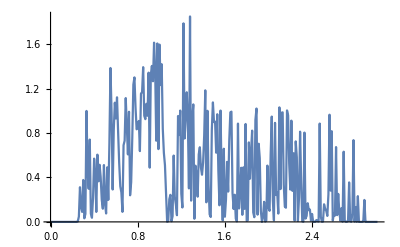

```mathematica
ListLinePlot[Table[{ω,m6pair24[ω]},{ω,Range[0,3,0.01]}]]
```

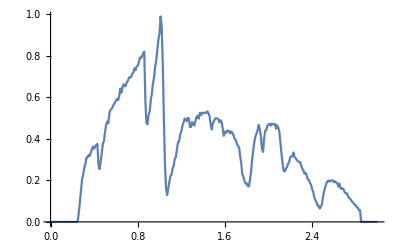

```mathematica
ListPlot[%98,Joined->True]
```

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m6pair24.dat",%21]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m6pair24.dat

```mathematica
m5[ω_,ϵ1_]:=Block[{Tin=T1[1,7],T=ρ[1,7],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}],a1=RandomSample[Flatten[RandomSample[l,1]],2],a2=RandomSample[Flatten[RandomSample[l,1]],2],a3=RandomSample[Flatten[RandomSample[l1,1]],2],a4=RandomSample[Flatten[RandomSample[l1,1]],2]},
imp1:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];imp9:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a1[[1]],a1[[1]]},{a1[[2]],a1[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a2[[1]],a2[[1]]},{a2[[2]],a2[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a3[[1]],a3[[1]]},{a3[[2]],a3[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a4[[1]],a4[[1]]},{a4[[2]],a4[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra1:=Block[{J=SL[ω,0.0001,1,0,7]},
b=Block[{},
lista={RandomSample[{imp3,imp12,imp8,imp11,imp1,imp4,imp12,imp10,imp,imp1,imp4,imp,imp5,imp3,imp5,imp10,imp,imp1,imp3,imp8,imp12,imp7,imp2,imp3,imp,imp13,imp7,imp13,imp2,imp6,imp,imp14,imp4,imp,imp,imp14,imp6,imp11,imp,imp2,imp7,imp7,imp10,imp13,imp14,imp2,imp6,imp,imp13,imp,imp3,imp8,imp4,imp14,imp2,imp9,imp8,imp2,imp,imp1,imp1,imp,imp11,imp11,imp,imp7,imp6,imp5,imp9,imp,imp14,imp4,imp11,imp10,imp9,imp5,imp6,imp8,imp10,imp,imp,imp,imp9,imp,imp3,imp9,imp13,imp1,imp5,imp,imp5,imp6,imp,imp,imp12,imp8,imp7,imp,imp12,imp4}]};
sl1= Block[{},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.J.T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-J.T.sl1.T].J;gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= J.T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0,7],tr[ω,0.0001,1,0,7],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
tr1];
b];
tra1]
```

```mathematica
m5pair20= Compile[{ω},m5[ω,0.5],CompilationTarget->"C",CompilationOptions->{"InlineExternalDefinitions" -> True},CompilationOptions->{"ExpressionOptimization" -> True},RuntimeOptions->"Quality"]
```

CompiledFunction[…]

```mathematica
Mean[ParallelTable[m5pair20[1],2000]]//AbsoluteTiming
```

{7.31625,0.942201}

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m5pair20.dat",%52]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m5pair20.dat

```mathematica
Table[{ω,Mean[ParallelTable[m5pair20[ω],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.79999×10^-7},{0.01,2.80692×10^-7},{0.02,2.82597×10^-7},{0.03,2.85101×10^-7},{0.04,2.87661×10^-7},{0.05,2.90988×10^-7},{0.06,2.95429×10^-7},{0.07,3.01806×10^-7},{0.08,3.0944×10^-7},{0.09,3.19462×10^-7},{0.1,3.33567×10^-7},{0.11,3.50156×10^-7},{0.12,3.7193×10^-7},{0.13,3.96209×10^-7},{0.14,4.30221×10^-7},{0.15,4.74627×10^-7},{0.16,5.30583×10^-7},{0.17,6.04018×10^-7},{0.18,6.97845×10^-7},{0.19,8.4909×10^-7},{0.2,1.07462×10^-6},{0.21,1.42939×10^-6},{0.22,2.10343×10^-6},{0.23,3.62157×10^-6},{0.24,9.77105×10^-6},{0.25,0.00236723},{0.26,0.0384159},{0.27,0.113305},{0.28,0.165953},{0.29,0.224051},{0.3,0.247253},{0.31,0.255403},{0.32,0.291845},{0.33,0.295229},{0.34,0.304981},{0.35,0.329161},{0.36,0.330325},{0.37,0.34437},{0.38,0.357994},{0.39,0.366451},{0.4,0.366745},{0.41,0.379754},{0.42,0.378707},{0.43,0.365915},{0.44,0.26996},{0.45,0.26732},{0.46,0.300034},{0.47,0.348771},{0.48,0.38881},{0.49,0.4028},{0.5,0.427099},{0.51,0.460464},{0.52,0.470669},{0.53,0.509376},{0.54,0.512793},{0.55,0.52503},{0.56,0.534484},{0.57,0.586608},{0.58,0.570416},{0.59,0.57938},{0.6,0.592783},{0.61,0.595501},{0.62,0.608686},{0.63,0.620247},{0.64,0.631048},{0.65,0.636336},{0.66,0.650697},{0.67,0.648738},{0.68,0.651797},{0.69,0.679166},{0.7,0.679266},{0.71,0.679122},{0.72,0.69335},{0.73,0.703131},{0.74,0.697809},{0.75,0.712203},{0.76,0.712852},{0.77,0.740982},{0.78,0.746339},{0.79,0.752578},{0.8,0.755135},{0.81,0.75516},{0.82,0.799161},{0.83,0.78624},{0.84,0.809168},{0.85,0.826372},{0.86,0.823807},{0.87,0.598573},{0.88,0.452219},{0.89,0.470398},{0.9,0.528211},{0.91,0.569658},{0.92,0.620421},{0.93,0.655026},{0.94,0.695044},{0.95,0.725535},{0.96,0.762388},{0.97,0.802153},{0.98,0.853343},{0.99,0.8882},{1.,0.93549},{1.01,0.996338},{1.02,0.931259},{1.03,0.781429},{1.04,0.497359},{1.05,0.286413},{1.06,0.154484},{1.07,0.136934},{1.08,0.163555},{1.09,0.186711},{1.1,0.221818},{1.11,0.240625},{1.12,0.266301},{1.13,0.263689},{1.14,0.291537},{1.15,0.323809},{1.16,0.348883},{1.17,0.359736},{1.18,0.392557},{1.19,0.403466},{1.2,0.419978},{1.21,0.444832},{1.22,0.459129},{1.23,0.466252},{1.24,0.463798},{1.25,0.47351},{1.26,0.502767},{1.27,0.479092},{1.28,0.465401},{1.29,0.476431},{1.3,0.494057},{1.31,0.476498},{1.32,0.485176},{1.33,0.490038},{1.34,0.50425},{1.35,0.494115},{1.36,0.501986},{1.37,0.501006},{1.38,0.513262},{1.39,0.516818},{1.4,0.519181},{1.41,0.528009},{1.42,0.50827},{1.43,0.51637},{1.44,0.508634},{1.45,0.517895},{1.46,0.49321},{1.47,0.444491},{1.48,0.440853},{1.49,0.456823},{1.5,0.468323},{1.51,0.472826},{1.52,0.482665},{1.53,0.495038},{1.54,0.482502},{1.55,0.460076},{1.56,0.476653},{1.57,0.44297},{1.58,0.42085},{1.59,0.401597},{1.6,0.4117},{1.61,0.415944},{1.62,0.414859},{1.63,0.413914},{1.64,0.408898},{1.65,0.40287},{1.66,0.39126},{1.67,0.395365},{1.68,0.382049},{1.69,0.377916},{1.7,0.360011},{1.71,0.344781},{1.72,0.339712},{1.73,0.328097},{1.74,0.300489},{1.75,0.288754},{1.76,0.259987},{1.77,0.219039},{1.78,0.227901},{1.79,0.192588},{1.8,0.191847},{1.81,0.168132},{1.82,0.17793},{1.83,0.188779},{1.84,0.229998},{1.85,0.285232},{1.86,0.327403},{1.87,0.368267},{1.88,0.387892},{1.89,0.403599},{1.9,0.406436},{1.91,0.404499},{1.92,0.399483},{1.93,0.360924},{1.94,0.288137},{1.95,0.329623},{1.96,0.357817},{1.97,0.386987},{1.98,0.394691},{1.99,0.403176},{2.,0.412032},{2.01,0.429331},{2.02,0.426818},{2.03,0.409615},{2.04,0.414724},{2.05,0.41668},{2.06,0.409864},{2.07,0.404151},{2.08,0.40063},{2.09,0.399062},{2.1,0.394855},{2.11,0.397271},{2.12,0.356704},{2.13,0.333729},{2.14,0.320113},{2.15,0.31801},{2.16,0.315562},{2.17,0.328261},{2.18,0.326251},{2.19,0.341583},{2.2,0.322924},{2.21,0.314366},{2.22,0.320861},{2.23,0.314742},{2.24,0.30506},{2.25,0.291597},{2.26,0.287846},{2.27,0.295921},{2.28,0.2789},{2.29,0.281493},{2.3,0.276376},{2.31,0.258698},{2.32,0.253669},{2.33,0.223117},{2.34,0.216248},{2.35,0.22687},{2.36,0.20848},{2.37,0.202475},{2.38,0.187706},{2.39,0.17578},{2.4,0.155317},{2.41,0.137401},{2.42,0.121222},{2.43,0.121945},{2.44,0.100235},{2.45,0.0848776},{2.46,0.0769942},{2.47,0.0615364},{2.48,0.0692467},{2.49,0.0863096},{2.5,0.120473},{2.51,0.125794},{2.52,0.152293},{2.53,0.159843},{2.54,0.164996},{2.55,0.185942},{2.56,0.170537},{2.57,0.17489},{2.58,0.166068},{2.59,0.170657},{2.6,0.168844},{2.61,0.161252},{2.62,0.160967},{2.63,0.164964},{2.64,0.142406},{2.65,0.158223},{2.66,0.150127},{2.67,0.14041},{2.68,0.145337},{2.69,0.149446},{2.7,0.126514},{2.71,0.129056},{2.72,0.125207},{2.73,0.114596},{2.74,0.107309},{2.75,0.0983012},{2.76,0.10354},{2.77,0.0920221},{2.78,0.0931801},{2.79,0.0844691},{2.8,0.0679696},{2.81,0.0740252},{2.82,0.0627804},{2.83,0.0668548},{2.84,0.0572662},{2.85,0.000376605},{2.86,0.0000163172},{2.87,4.96478×10^-6},{2.88,2.35226×10^-6},{2.89,1.36388×10^-6},{2.9,8.87756×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
m4[ω_,ϵ1_]:=Block[{Tin=T1[1,7],T=ρ[1,7],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}],a1=RandomSample[Flatten[RandomSample[l,1]],2],a2=RandomSample[Flatten[RandomSample[l,1]],2],a3=RandomSample[Flatten[RandomSample[l1,1]],2],a4=RandomSample[Flatten[RandomSample[l1,1]],2]},
imp1:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];imp9:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a1[[1]],a1[[1]]},{a1[[2]],a1[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a2[[1]],a2[[1]]},{a2[[2]],a2[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a3[[1]],a3[[1]]},{a3[[2]],a3[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a4[[1]],a4[[1]]},{a4[[2]],a4[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra1:=Block[{J=SL[ω,0.0001,1,0,7]},
b=Block[{},
lista={RandomSample[{imp1,imp7,imp2,imp11,imp12,imp5,imp12,imp,imp13,imp6,imp7,imp,imp2,imp1,imp4,imp12,imp2,imp9,imp2,imp6,imp9,imp2,imp5,imp,imp5,imp13,imp11,imp6,imp10,imp9,imp1,imp5,imp3,imp7,imp14,imp8,imp,imp,imp3,imp,imp7,imp7,imp6,imp1,imp4,imp8,imp14,imp9,imp11,imp5,imp2,imp,imp7,imp4,imp4,imp1,imp3,imp,imp8,imp2,imp3,imp10,imp14,imp,imp4,imp1,imp,imp8,imp,imp8,imp6,imp6,imp1,imp7,imp,imp10,imp8,imp12,imp,imp4,imp3,imp,imp,imp,imp10,imp,imp9,imp,imp5,imp6,imp13,imp13,imp4,imp3,imp10,imp11,imp3,imp14,imp5,imp8}]};
sl1= Block[{},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.J.T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-J.T.sl1.T].J;gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= J.T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0,7],tr[ω,0.0001,1,0,7],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
tr1];
b];
tra1]
```

```mathematica
m4pair16= Compile[{ω},m4[ω,0.5],CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True}]
```

CompiledFunction[…]

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m4pair16.dat",%55]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m4pair16.dat

```mathematica
Table[{ω,Mean[ParallelTable[m4pair16[ω],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.8×10^-7},{0.01,2.80691×10^-7},{0.02,2.82583×10^-7},{0.03,2.85082×10^-7},{0.04,2.87588×10^-7},{0.05,2.9059×10^-7},{0.06,2.94927×10^-7},{0.07,3.0102×10^-7},{0.08,3.08802×10^-7},{0.09,3.19739×10^-7},{0.1,3.3305×10^-7},{0.11,3.49209×10^-7},{0.12,3.69856×10^-7},{0.13,3.95561×10^-7},{0.14,4.28438×10^-7},{0.15,4.71797×10^-7},{0.16,5.27179×10^-7},{0.17,5.95029×10^-7},{0.18,7.01435×10^-7},{0.19,8.46334×10^-7},{0.2,1.0603×10^-6},{0.21,1.4065×10^-6},{0.22,2.10238×10^-6},{0.23,3.51788×10^-6},{0.24,8.89808×10^-6},{0.25,0.00189465},{0.26,0.0438245},{0.27,0.108786},{0.28,0.173306},{0.29,0.233159},{0.3,0.251635},{0.31,0.272843},{0.32,0.291438},{0.33,0.303864},{0.34,0.327346},{0.35,0.325012},{0.36,0.352695},{0.37,0.34182},{0.38,0.36215},{0.39,0.365249},{0.4,0.375842},{0.41,0.381524},{0.42,0.381465},{0.43,0.363792},{0.44,0.286039},{0.45,0.257171},{0.46,0.304108},{0.47,0.344449},{0.48,0.373596},{0.49,0.414759},{0.5,0.443476},{0.51,0.472808},{0.52,0.490993},{0.53,0.523466},{0.54,0.526665},{0.55,0.538442},{0.56,0.562967},{0.57,0.573978},{0.58,0.586315},{0.59,0.600629},{0.6,0.606126},{0.61,0.608995},{0.62,0.613966},{0.63,0.625177},{0.64,0.629885},{0.65,0.659129},{0.66,0.647633},{0.67,0.650407},{0.68,0.668074},{0.69,0.665667},{0.7,0.680382},{0.71,0.667169},{0.72,0.696166},{0.73,0.701167},{0.74,0.714215},{0.75,0.724358},{0.76,0.717118},{0.77,0.730243},{0.78,0.750269},{0.79,0.762218},{0.8,0.750167},{0.81,0.767868},{0.82,0.79179},{0.83,0.791568},{0.84,0.795537},{0.85,0.8407},{0.86,0.811122},{0.87,0.589509},{0.88,0.477628},{0.89,0.497162},{0.9,0.539335},{0.91,0.560883},{0.92,0.618889},{0.93,0.646812},{0.94,0.703983},{0.95,0.743637},{0.96,0.783532},{0.97,0.817475},{0.98,0.872503},{0.99,0.890815},{1.,0.964718},{1.01,1.03132},{1.02,0.958937},{1.03,0.784479},{1.04,0.493648},{1.05,0.28478},{1.06,0.148},{1.07,0.130144},{1.08,0.154092},{1.09,0.181793},{1.1,0.219717},{1.11,0.232804},{1.12,0.266885},{1.13,0.268399},{1.14,0.289182},{1.15,0.324534},{1.16,0.353468},{1.17,0.379698},{1.18,0.408093},{1.19,0.427594},{1.2,0.442156},{1.21,0.441896},{1.22,0.475668},{1.23,0.465553},{1.24,0.499598},{1.25,0.492732},{1.26,0.495895},{1.27,0.497158},{1.28,0.474519},{1.29,0.47132},{1.3,0.491161},{1.31,0.486061},{1.32,0.484947},{1.33,0.490001},{1.34,0.494997},{1.35,0.502312},{1.36,0.502552},{1.37,0.523802},{1.38,0.496137},{1.39,0.521205},{1.4,0.51361},{1.41,0.516727},{1.42,0.521178},{1.43,0.519594},{1.44,0.521576},{1.45,0.517906},{1.46,0.478865},{1.47,0.432844},{1.48,0.434221},{1.49,0.462141},{1.5,0.463606},{1.51,0.471029},{1.52,0.446012},{1.53,0.471401},{1.54,0.467779},{1.55,0.477378},{1.56,0.47349},{1.57,0.435209},{1.58,0.401706},{1.59,0.398762},{1.6,0.399584},{1.61,0.408442},{1.62,0.403504},{1.63,0.407919},{1.64,0.417147},{1.65,0.398817},{1.66,0.400064},{1.67,0.391077},{1.68,0.379689},{1.69,0.358451},{1.7,0.363192},{1.71,0.35136},{1.72,0.334732},{1.73,0.339671},{1.74,0.309984},{1.75,0.290679},{1.76,0.245414},{1.77,0.232195},{1.78,0.20937},{1.79,0.192733},{1.8,0.190465},{1.81,0.171947},{1.82,0.16517},{1.83,0.184728},{1.84,0.242044},{1.85,0.287992},{1.86,0.322545},{1.87,0.355622},{1.88,0.372611},{1.89,0.381929},{1.9,0.38604},{1.91,0.396352},{1.92,0.385332},{1.93,0.335093},{1.94,0.281861},{1.95,0.279887},{1.96,0.344938},{1.97,0.362144},{1.98,0.40235},{1.99,0.38754},{2.,0.40001},{2.01,0.386839},{2.02,0.402714},{2.03,0.392861},{2.04,0.404995},{2.05,0.382821},{2.06,0.399584},{2.07,0.381205},{2.08,0.402736},{2.09,0.385269},{2.1,0.386331},{2.11,0.37006},{2.12,0.358695},{2.13,0.308035},{2.14,0.296355},{2.15,0.305687},{2.16,0.326989},{2.17,0.317469},{2.18,0.320042},{2.19,0.319396},{2.2,0.330066},{2.21,0.325702},{2.22,0.31174},{2.23,0.307979},{2.24,0.295244},{2.25,0.303015},{2.26,0.287467},{2.27,0.281279},{2.28,0.280579},{2.29,0.267133},{2.3,0.262039},{2.31,0.250589},{2.32,0.243932},{2.33,0.222909},{2.34,0.229463},{2.35,0.209439},{2.36,0.19826},{2.37,0.200709},{2.38,0.18331},{2.39,0.179492},{2.4,0.158583},{2.41,0.141979},{2.42,0.136783},{2.43,0.112379},{2.44,0.102691},{2.45,0.0850641},{2.46,0.0690887},{2.47,0.0720482},{2.48,0.0730504},{2.49,0.0910647},{2.5,0.117132},{2.51,0.134941},{2.52,0.147925},{2.53,0.159658},{2.54,0.165507},{2.55,0.175303},{2.56,0.188465},{2.57,0.17671},{2.58,0.171365},{2.59,0.169208},{2.6,0.164535},{2.61,0.166603},{2.62,0.160671},{2.63,0.164237},{2.64,0.157078},{2.65,0.155748},{2.66,0.160684},{2.67,0.143188},{2.68,0.15164},{2.69,0.140604},{2.7,0.125463},{2.71,0.125514},{2.72,0.127766},{2.73,0.126517},{2.74,0.12152},{2.75,0.117953},{2.76,0.101833},{2.77,0.100551},{2.78,0.0941727},{2.79,0.0840063},{2.8,0.0867104},{2.81,0.0877845},{2.82,0.0738953},{2.83,0.0687902},{2.84,0.0540575},{2.85,0.000385361},{2.86,0.0000163656},{2.87,4.9717×10^-6},{2.88,2.35273×10^-6},{2.89,1.36412×10^-6},{2.9,8.87818×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
m3[ω_,ϵ1_]:=Block[{Tin=T1[1,7],T=ρ[1,7],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}],a1=RandomSample[Flatten[RandomSample[l,1]],2],a2=RandomSample[Flatten[RandomSample[l,1]],2],a3=RandomSample[Flatten[RandomSample[l1,1]],2],a4=RandomSample[Flatten[RandomSample[l1,1]],2]},
imp1:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];imp9:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a1[[1]],a1[[1]]},{a1[[2]],a1[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a2[[1]],a2[[1]]},{a2[[2]],a2[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a3[[1]],a3[[1]]},{a3[[2]],a3[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a4[[1]],a4[[1]]},{a4[[2]],a4[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra1:=Block[{J=SL[ω,0.0001,1,0,7]},
b=Block[{},
lista={RandomSample[{imp8,imp11,imp,imp8,imp9,imp1,imp10,imp3,imp9,imp7,imp2,imp6,imp7,imp1,imp12,imp3,imp10,imp8,imp5,imp3,imp6,imp5,imp14,imp2,imp6,imp14,imp,imp1,imp1,imp8,imp,imp,imp,imp6,imp1,imp5,imp,imp13,imp3,imp4,imp,imp,imp2,imp8,imp12,imp11,imp3,imp9,imp2,imp1,imp6,imp7,imp1,imp,imp2,imp3,imp3,imp9,imp7,imp4,imp5,imp7,imp8,imp14,imp,imp,imp7,imp10,imp4,imp,imp11,imp4,imp5,imp13,imp8,imp10,imp12,imp10,imp6,imp13,imp2,imp4,imp5,imp7,imp6,imp2,imp8,imp4,imp4,imp,imp5,imp3,imp6,imp1,imp7,imp5,imp4,imp,imp9,imp2}]};
sl1= Block[{},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.J.T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-J.T.sl1.T].J;gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= J.T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0,7],tr[ω,0.0001,1,0,7],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
tr1];
b];
tra1]
```

```mathematica
Clear[m3pair12]
```

```mathematica
m3pair12= Compile[{ω},m3[ω,0.5],CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True}]
```

CompiledFunction[…]

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m3pair12.dat",%59]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m3pair12.dat

```mathematica
Table[{ω,Mean[ParallelTable[m3pair12[ω],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.8×10^-7},{0.01,2.80683×10^-7},{0.02,2.82585×10^-7},{0.03,2.85034×10^-7},{0.04,2.87476×10^-7},{0.05,2.90406×10^-7},{0.06,2.94436×10^-7},{0.07,3.00426×10^-7},{0.08,3.08448×10^-7},{0.09,3.18728×10^-7},{0.1,3.31841×10^-7},{0.11,3.4752×10^-7},{0.12,3.68309×10^-7},{0.13,3.94941×10^-7},{0.14,4.28157×10^-7},{0.15,4.70616×10^-7},{0.16,5.19192×10^-7},{0.17,5.92654×10^-7},{0.18,6.94294×10^-7},{0.19,8.31908×10^-7},{0.2,1.04025×10^-6},{0.21,1.38817×10^-6},{0.22,2.01333×10^-6},{0.23,3.29895×10^-6},{0.24,8.59595×10^-6},{0.25,0.00114685},{0.26,0.0427611},{0.27,0.109444},{0.28,0.189555},{0.29,0.231839},{0.3,0.260319},{0.31,0.290808},{0.32,0.323088},{0.33,0.327226},{0.34,0.346395},{0.35,0.335292},{0.36,0.352405},{0.37,0.362994},{0.38,0.362933},{0.39,0.368622},{0.4,0.387237},{0.41,0.393227},{0.42,0.397969},{0.43,0.379214},{0.44,0.30273},{0.45,0.246939},{0.46,0.305457},{0.47,0.354762},{0.48,0.386011},{0.49,0.420461},{0.5,0.449136},{0.51,0.476028},{0.52,0.521965},{0.53,0.52633},{0.54,0.542974},{0.55,0.533174},{0.56,0.561772},{0.57,0.586183},{0.58,0.589244},{0.59,0.6},{0.6,0.626152},{0.61,0.61194},{0.62,0.622467},{0.63,0.63098},{0.64,0.641672},{0.65,0.640709},{0.66,0.647718},{0.67,0.664798},{0.68,0.662823},{0.69,0.671322},{0.7,0.683552},{0.71,0.681727},{0.72,0.695114},{0.73,0.704445},{0.74,0.712379},{0.75,0.724645},{0.76,0.7337},{0.77,0.740421},{0.78,0.758168},{0.79,0.75529},{0.8,0.783014},{0.81,0.775955},{0.82,0.780634},{0.83,0.792827},{0.84,0.806428},{0.85,0.828437},{0.86,0.809122},{0.87,0.608956},{0.88,0.476565},{0.89,0.492122},{0.9,0.548618},{0.91,0.588332},{0.92,0.633987},{0.93,0.672441},{0.94,0.72507},{0.95,0.770978},{0.96,0.813552},{0.97,0.862997},{0.98,0.892636},{0.99,0.923578},{1.,0.98635},{1.01,1.0442},{1.02,0.99881},{1.03,0.770305},{1.04,0.50536},{1.05,0.256732},{1.06,0.149448},{1.07,0.126154},{1.08,0.169394},{1.09,0.183401},{1.1,0.219422},{1.11,0.245907},{1.12,0.264708},{1.13,0.274071},{1.14,0.309452},{1.15,0.343535},{1.16,0.362524},{1.17,0.390395},{1.18,0.405484},{1.19,0.426688},{1.2,0.444289},{1.21,0.449286},{1.22,0.46207},{1.23,0.477541},{1.24,0.496539},{1.25,0.502708},{1.26,0.504318},{1.27,0.493671},{1.28,0.49378},{1.29,0.482239},{1.3,0.482901},{1.31,0.48191},{1.32,0.493541},{1.33,0.482023},{1.34,0.516419},{1.35,0.50286},{1.36,0.499511},{1.37,0.504412},{1.38,0.521652},{1.39,0.522066},{1.4,0.52114},{1.41,0.522653},{1.42,0.525306},{1.43,0.53597},{1.44,0.521722},{1.45,0.511649},{1.46,0.484073},{1.47,0.426143},{1.48,0.424395},{1.49,0.459105},{1.5,0.458943},{1.51,0.469409},{1.52,0.461402},{1.53,0.45963},{1.54,0.465471},{1.55,0.478678},{1.56,0.449648},{1.57,0.431049},{1.58,0.391721},{1.59,0.381823},{1.6,0.38994},{1.61,0.408173},{1.62,0.392764},{1.63,0.420451},{1.64,0.405683},{1.65,0.39361},{1.66,0.40203},{1.67,0.382596},{1.68,0.363308},{1.69,0.362766},{1.7,0.359442},{1.71,0.334791},{1.72,0.335594},{1.73,0.31976},{1.74,0.308899},{1.75,0.277921},{1.76,0.251287},{1.77,0.224189},{1.78,0.205127},{1.79,0.189482},{1.8,0.166769},{1.81,0.167165},{1.82,0.163853},{1.83,0.195916},{1.84,0.2298},{1.85,0.275376},{1.86,0.319051},{1.87,0.339833},{1.88,0.384738},{1.89,0.358877},{1.9,0.380578},{1.91,0.371585},{1.92,0.362626},{1.93,0.326202},{1.94,0.264282},{1.95,0.270363},{1.96,0.335962},{1.97,0.354809},{1.98,0.372766},{1.99,0.384714},{2.,0.385338},{2.01,0.386688},{2.02,0.383516},{2.03,0.383982},{2.04,0.382729},{2.05,0.390654},{2.06,0.396713},{2.07,0.390153},{2.08,0.396045},{2.09,0.379129},{2.1,0.373196},{2.11,0.370351},{2.12,0.342518},{2.13,0.308423},{2.14,0.281891},{2.15,0.298319},{2.16,0.298576},{2.17,0.312693},{2.18,0.315589},{2.19,0.313584},{2.2,0.314949},{2.21,0.306661},{2.22,0.306209},{2.23,0.295621},{2.24,0.295208},{2.25,0.28701},{2.26,0.280587},{2.27,0.276711},{2.28,0.285288},{2.29,0.265428},{2.3,0.270472},{2.31,0.246038},{2.32,0.256971},{2.33,0.233692},{2.34,0.231991},{2.35,0.203675},{2.36,0.211779},{2.37,0.196804},{2.38,0.18163},{2.39,0.170093},{2.4,0.178719},{2.41,0.156504},{2.42,0.129575},{2.43,0.113914},{2.44,0.107515},{2.45,0.0904535},{2.46,0.0737424},{2.47,0.0725631},{2.48,0.0686564},{2.49,0.0906812},{2.5,0.10795},{2.51,0.143309},{2.52,0.160865},{2.53,0.167663},{2.54,0.168925},{2.55,0.184256},{2.56,0.180925},{2.57,0.169392},{2.58,0.182817},{2.59,0.177902},{2.6,0.171717},{2.61,0.175211},{2.62,0.174069},{2.63,0.169724},{2.64,0.160211},{2.65,0.168773},{2.66,0.15862},{2.67,0.158681},{2.68,0.153373},{2.69,0.146667},{2.7,0.155995},{2.71,0.143813},{2.72,0.137942},{2.73,0.128396},{2.74,0.124103},{2.75,0.119612},{2.76,0.124181},{2.77,0.101125},{2.78,0.112043},{2.79,0.0995478},{2.8,0.0884955},{2.81,0.0856388},{2.82,0.0790188},{2.83,0.066242},{2.84,0.0684653},{2.85,0.000404386},{2.86,0.0000164478},{2.87,4.96964×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

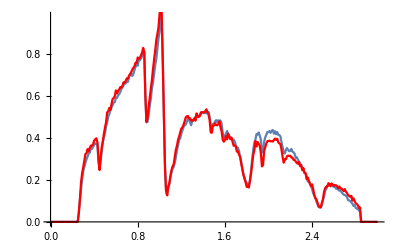

```mathematica
Show[ListPlot[%21,Joined->True],ListPlot[%59,Joined->True,PlotStyle->Red]]
```

```mathematica
misfit[ϵ1_,x_,y_]:=Block[{Tin=T1[1,7],T=ρ[1,7],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}],a1=RandomSample[Flatten[RandomSample[l,1]],2],a2=RandomSample[Flatten[RandomSample[l,1]],2],a3=RandomSample[Flatten[RandomSample[l1,1]],2],a4=RandomSample[Flatten[RandomSample[l1,1]],2],imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14,imp},
imp1:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];imp9:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a1[[1]],a1[[1]]},{a1[[2]],a1[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a2[[1]],a2[[1]]},{a2[[2]],a2[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a3[[1]],a3[[1]]},{a3[[2]],a3[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{a4[[1]],a4[[1]]},{a4[[2]],a4[[2]]}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Block[{κ=β[ω,0.0001,1,0,7]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra1:=Block[{J=SL[ω,0.0001,1,0,7]},
b=Block[{},
lista={{imp8,imp5,imp,imp5,imp,imp11,imp3,imp7,imp4,imp7,imp,imp1,imp5,imp8,imp11,imp12,imp14,imp6,imp8,imp5,imp6,imp10,imp8,imp4,imp4,imp1,imp13,imp,imp,imp4,imp7,imp2,imp10,imp4,imp6,imp2,imp9,imp8,imp7,imp,imp13,imp3,imp5,imp3,imp4,imp,imp14,imp10,imp7,imp3,imp3,imp12,imp,imp3,imp2,imp4,imp13,imp14,imp,imp5,imp1,imp9,imp6,imp1,imp6,imp2,imp8,imp7,imp,imp3,imp2,imp7,imp9,imp7,imp10,imp11,imp6,imp1,imp4,imp2,imp,imp6,imp3,imp8,imp1,imp5,imp1,imp,imp9,imp8,imp9,imp,imp1,imp6,imp10,imp2,imp,imp12,imp5,imp2}};
sl1= Block[{},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];
Il1:=Inverse[IdentityMatrix[14]-sl1.T.J.T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-J.T.sl1.T].J;gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= J.T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0,7],tr[ω,0.0001,1,0,7],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
tr1];
b];
m=Table[{ω,tra1},{ω,Range[0,3,0.01]}];
υ=Module[{},
ρ1:=Module[{B1=Transpose[{m[[1;;300]][[;;,1]],100(m[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/7imp/7imp5.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ2:=Module[{B1=Transpose[{m[[1;;300]][[;;,1]],100(m[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m1pair4.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m[[1;;300]][[;;,1]],100(m[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m2pair8.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m[[1;;300]][[;;,1]],100(m[[1;;300,2]]- Import["/home/shardulmukim//PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m3pair12.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m[[1;;300]][[;;,1]],100(m[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m4pair16.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m[[1;;300]][[;;,1]],100(m[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m5pair20.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m[[1;;300]][[;;,1]],100(m[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m6pair24.dat"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7}];
υ]
```

```mathematica
ParallelTable[misfit[0.5,2.98,0],250]
```

{{0.105373,0.104727,0.105186,0.104473,0.104679,0.1052},{0.112684,0.112513,0.112001,0.112041,0.111928,0.112108},{0.10596,0.104225,0.103198,0.102791,0.102173,0.1013},{0.116171,0.115852,0.115359,0.115044,0.114595,0.114827},{0.105623,0.105851,0.106332,0.105951,0.10606,0.106649},{0.119881,0.120032,0.120708,0.120197,0.120521,0.121012},{0.110073,0.109412,0.110062,0.110509,0.110139,0.111116},{0.107428,0.106309,0.105615,0.1055,0.105461,0.10496},{0.0888859,0.0894432,0.0903427,0.0905957,0.0909845,0.0922584},{0.119014,0.11903,0.118414,0.11817,0.117663,0.117955},{0.116566,0.117642,0.118907,0.118902,0.119776,0.121134},{0.112559,0.112712,0.112327,0.113049,0.112906,0.113053},{0.123333,0.12497,0.126429,0.126797,0.127329,0.127747},{0.104584,0.105351,0.106771,0.107211,0.106989,0.107976},{0.120308,0.120945,0.120571,0.121185,0.121821,0.122495},{0.107591,0.10712,0.107699,0.10724,0.107353,0.107631},{0.152152,0.154848,0.156306,0.157006,0.157849,0.159275},{0.121384,0.121815,0.120769,0.121079,0.121075,0.120633},{0.100334,0.100955,0.100443,0.101098,0.10141,0.102121},{0.109894,0.110107,0.110895,0.110968,0.110874,0.111497},{0.105141,0.106003,0.106557,0.106744,0.107109,0.107964},{0.138163,0.141756,0.143823,0.14638,0.146984,0.149513},{0.0968408,0.0967819,0.0961414,0.0969668,0.0972794,0.0980236},{0.107662,0.107103,0.106548,0.106321,0.105512,0.106134},{0.0976165,0.0978537,0.0980595,0.0982435,0.0990271,0.100036},{0.100089,0.100767,0.101606,0.102183,0.102863,0.103548},{0.0861016,0.0856706,0.0855849,0.0860262,0.086788,0.0871255},{0.112295,0.111709,0.111304,0.110764,0.110413,0.110322},{0.117855,0.117995,0.118181,0.118406,0.118497,0.119142},{0.12221,0.121481,0.120932,0.120788,0.120782,0.12086},{0.0968584,0.0960787,0.0952884,0.0952739,0.0957014,0.0953517},{0.113401,0.112793,0.112917,0.113142,0.113509,0.1135},{0.0924525,0.0904149,0.0898607,0.08945,0.0895398,0.089705},{0.114959,0.116065,0.116946,0.117283,0.117781,0.118814},{0.123933,0.125994,0.126643,0.127288,0.128045,0.128636},{0.0949822,0.0951264,0.0952314,0.0960133,0.0959903,0.0968252},{0.108284,0.108519,0.107709,0.107861,0.107517,0.108003},{0.0997233,0.098617,0.0988305,0.0985648,0.0984503,0.0983923},{0.138559,0.138617,0.137891,0.137806,0.13739,0.137172},{0.118748,0.119314,0.120476,0.121457,0.122039,0.123191},{0.146671,0.14816,0.149479,0.150535,0.150209,0.151462},{0.107723,0.107965,0.108431,0.108595,0.109484,0.109642},{0.133308,0.131471,0.129211,0.127601,0.126354,0.125027},{0.0947519,0.0932067,0.0931887,0.0928955,0.0926606,0.0932946},{0.1174,0.116694,0.115599,0.11461,0.114278,0.113837},{0.0958661,0.0960352,0.0958971,0.0961074,0.0969108,0.0973054},{0.122738,0.123536,0.123311,0.124019,0.124727,0.124189},{0.101973,0.100566,0.0988116,0.0991745,0.0983396,0.0976387},{0.0972175,0.0980056,0.0978522,0.0984895,0.099403,0.0996282},{0.104593,0.104538,0.104425,0.104063,0.10448,0.105301},{0.106253,0.10639,0.106392,0.106634,0.106169,0.106554},{0.102691,0.101867,0.101571,0.101067,0.101538,0.101437},{0.116818,0.117205,0.118411,0.119314,0.120682,0.12124},{0.1014,0.101902,0.101642,0.102604,0.102483,0.102902},{0.103161,0.103246,0.103268,0.103052,0.103191,0.103056},{0.117378,0.118561,0.118788,0.119757,0.119994,0.120696},{0.135582,0.134763,0.133396,0.132805,0.131861,0.13166},{0.112851,0.112292,0.1127,0.11293,0.111934,0.112055},{0.105679,0.104753,0.105253,0.105614,0.10612,0.106318},{0.102778,0.102981,0.103737,0.104069,0.10504,0.10628},{0.0997721,0.10017,0.0997905,0.100046,0.100565,0.100549},{0.112817,0.113095,0.112392,0.113124,0.113114,0.113758},{0.124671,0.125132,0.125571,0.126281,0.126447,0.126935},{0.0935042,0.0936297,0.0940146,0.0937999,0.0941227,0.094949},{0.101836,0.100916,0.101011,0.101139,0.100448,0.101057},{0.0966869,0.0956949,0.0953953,0.0949728,0.0951755,0.0945404},{0.106143,0.104732,0.104147,0.104004,0.103207,0.102786},{0.098781,0.0989323,0.0995962,0.100814,0.100903,0.101536},{0.117284,0.115463,0.114476,0.114471,0.114184,0.114096},{0.110437,0.110714,0.111804,0.112054,0.112438,0.113008},{0.111631,0.112311,0.111589,0.111266,0.111888,0.11237},{0.0973452,0.0960979,0.0970328,0.0972296,0.0969394,0.097834},{0.125426,0.125655,0.125808,0.126253,0.125592,0.126405},{0.109088,0.107854,0.106321,0.105844,0.105065,0.10461},{0.109592,0.110409,0.110807,0.111525,0.112891,0.114159},{0.11492,0.113618,0.112472,0.111949,0.11143,0.111248},{0.101492,0.101906,0.101809,0.102091,0.101891,0.102054},{0.114228,0.113977,0.113692,0.114082,0.11417,0.114237},{0.111176,0.110795,0.110852,0.11108,0.111141,0.111534},{0.112972,0.114594,0.11491,0.115422,0.116684,0.11715},{0.119939,0.119359,0.11953,0.119324,0.119116,0.119329},{0.100588,0.0996612,0.0994081,0.0995221,0.100028,0.100248},{0.109763,0.108921,0.108436,0.107876,0.108256,0.107529},{0.10605,0.106191,0.106338,0.106568,0.107299,0.107621},{0.121897,0.122439,0.122201,0.122429,0.12228,0.122233},{0.119327,0.119957,0.120518,0.120897,0.121203,0.12156},{0.111325,0.111377,0.110339,0.110164,0.110013,0.110565},{0.118905,0.117903,0.11764,0.11701,0.116122,0.115782},{0.109137,0.108895,0.109203,0.109085,0.109349,0.109451},{0.103798,0.103455,0.103519,0.103523,0.10366,0.104435},{0.0956944,0.0942445,0.093089,0.0926589,0.092751,0.0921961},{0.113503,0.113177,0.113424,0.113377,0.113404,0.114283},{0.103801,0.103156,0.103334,0.103541,0.103777,0.104058},{0.113189,0.112262,0.112247,0.111989,0.111326,0.11168},{0.100599,0.0987602,0.0978788,0.0970499,0.0962795,0.0950933},{0.113774,0.115631,0.116616,0.11728,0.119202,0.119777},{0.120747,0.120854,0.120986,0.121421,0.120509,0.1212},{0.106538,0.106308,0.106982,0.10736,0.107811,0.108596},{0.129869,0.129296,0.127714,0.128122,0.1281,0.127873},{0.0956165,0.0944113,0.0942592,0.0940281,0.0937361,0.0939099},{0.113113,0.112395,0.112386,0.111808,0.112121,0.111781},{0.100652,0.101472,0.101686,0.102838,0.103212,0.103595},{0.120433,0.120932,0.12119,0.121247,0.121163,0.121518},{0.102894,0.103597,0.102912,0.103252,0.104084,0.104323},{0.108772,0.109794,0.110165,0.110284,0.110366,0.111309},{0.113478,0.113565,0.114346,0.113979,0.115337,0.115408},{0.103088,0.104395,0.10378,0.104979,0.10554,0.106366},{0.151124,0.151771,0.1526,0.153238,0.152294,0.153405},{0.123133,0.124851,0.125423,0.126766,0.12821,0.128821},{0.115003,0.114457,0.114016,0.114191,0.114117,0.114385},{0.109557,0.10905,0.10979,0.109401,0.109796,0.109843},{0.107758,0.108512,0.110191,0.111264,0.112225,0.113164},{0.11421,0.11236,0.111708,0.111985,0.111046,0.11128},{0.112024,0.111764,0.111055,0.110764,0.110322,0.111095},{0.106048,0.106286,0.106268,0.106963,0.107192,0.107829},{0.111426,0.10992,0.109325,0.108551,0.108156,0.108491},{0.105424,0.104798,0.104194,0.104837,0.104545,0.104722},{0.0956526,0.09586,0.0964979,0.095982,0.0961159,0.0967312},{0.106118,0.105512,0.105627,0.105477,0.10501,0.104984},{0.117199,0.116273,0.116023,0.115764,0.116277,0.116759},{0.121197,0.118464,0.117151,0.115771,0.115313,0.114249},{0.109618,0.11064,0.111968,0.112682,0.114069,0.11522},{0.107275,0.106274,0.104837,0.104686,0.104108,0.103924},{0.0989586,0.0999843,0.1006,0.101631,0.102392,0.1029},{0.110322,0.10983,0.109547,0.109863,0.109231,0.109559},{0.0983942,0.0999848,0.100061,0.100179,0.101175,0.102268},{0.101797,0.101379,0.101499,0.101563,0.101834,0.10195},{0.157506,0.16166,0.16382,0.165357,0.167761,0.168565},{0.107385,0.106948,0.107579,0.108445,0.10873,0.109408},{0.0986121,0.100068,0.0999686,0.101172,0.101677,0.102324},{0.128381,0.126915,0.125521,0.12563,0.125523,0.125036},{0.106713,0.106816,0.107912,0.10836,0.109175,0.110478},{0.111422,0.111037,0.111314,0.112219,0.112431,0.113013},{0.0932211,0.0928041,0.093138,0.0931758,0.0940096,0.0946437},{0.0999847,0.0999599,0.0993376,0.0997933,0.100164,0.100582},{0.115929,0.116797,0.11818,0.118761,0.118361,0.119271},{0.123894,0.123136,0.123174,0.122866,0.122283,0.121909},{0.104613,0.102847,0.103121,0.102617,0.102005,0.101865},{0.111997,0.111468,0.112157,0.112485,0.112394,0.113837},{0.107565,0.107401,0.107546,0.107595,0.107722,0.107936},{0.110228,0.109637,0.109452,0.109466,0.108997,0.109271},{0.118604,0.116725,0.115173,0.114156,0.114048,0.112946},{0.101629,0.102332,0.103541,0.104098,0.104831,0.10601},{0.107987,0.108995,0.109281,0.110093,0.111339,0.112369},{0.108684,0.108091,0.107597,0.107282,0.10705,0.105786},{0.111624,0.111694,0.111305,0.111632,0.110589,0.110575},{0.100519,0.100208,0.0995007,0.0992598,0.0993923,0.0993464},{0.102098,0.101556,0.101011,0.100854,0.100854,0.100882},{0.0809237,0.0800761,0.0804598,0.0802672,0.0802113,0.0810163},{0.102453,0.102156,0.10284,0.103077,0.102978,0.10403},{0.111831,0.111494,0.111935,0.111549,0.112315,0.11264},{0.115825,0.117408,0.118132,0.119764,0.119577,0.121098},{0.124174,0.125122,0.125874,0.126596,0.127206,0.127665},{0.108317,0.107277,0.104936,0.104528,0.104212,0.103938},{0.1447,0.148069,0.149951,0.151927,0.152786,0.15439},{0.106881,0.105541,0.104316,0.103715,0.103655,0.103477},{0.12193,0.12034,0.119324,0.118934,0.11813,0.117727},{0.113411,0.113219,0.112819,0.113388,0.11346,0.113706},{0.122155,0.121571,0.121426,0.121389,0.121248,0.12153},{0.100643,0.0999104,0.0988066,0.0995083,0.0988473,0.0989984},{0.0993513,0.0988873,0.0979886,0.0975023,0.0978828,0.0975702},{0.100534,0.0993916,0.0974218,0.0974331,0.0976349,0.0970936},{0.117886,0.115832,0.114349,0.113445,0.112425,0.111758},{0.125441,0.124048,0.123235,0.122236,0.121761,0.121427},{0.114303,0.11354,0.113475,0.113982,0.113777,0.113477},{0.118135,0.117469,0.118145,0.118367,0.118356,0.118314},{0.126498,0.128483,0.129109,0.130209,0.130043,0.131455},{0.119435,0.118738,0.118261,0.118312,0.11792,0.118253},{0.119655,0.121341,0.121954,0.122993,0.123701,0.12395},{0.121337,0.121864,0.122916,0.123218,0.123473,0.123214},{0.126164,0.125845,0.125586,0.125636,0.125505,0.125795},{0.117022,0.118074,0.117673,0.117937,0.119245,0.11993},{0.114801,0.114493,0.114281,0.114431,0.114256,0.114288},{0.0999239,0.0984299,0.0982394,0.0981532,0.0980939,0.0986622},{0.123107,0.122907,0.122957,0.123466,0.123912,0.123941},{0.104378,0.103519,0.102712,0.102292,0.102509,0.102014},{0.115698,0.116135,0.115763,0.115803,0.11637,0.116368},{0.112013,0.110671,0.108794,0.109182,0.108885,0.108262},{0.117985,0.116922,0.116393,0.115152,0.114513,0.114371},{0.122102,0.122349,0.122706,0.122933,0.12364,0.123951},{0.100895,0.100185,0.0997567,0.099447,0.0995907,0.0992641},{0.128532,0.127623,0.128296,0.128014,0.128765,0.129482},{0.108872,0.107881,0.107258,0.106982,0.107617,0.107449},{0.122456,0.122326,0.122696,0.123426,0.122845,0.123446},{0.0946923,0.0938237,0.0944333,0.0934095,0.0936715,0.094154},{0.124151,0.124586,0.124233,0.124362,0.12465,0.124917},{0.0954102,0.0950942,0.094028,0.0948436,0.095145,0.0947337},{0.109669,0.11043,0.110801,0.111954,0.112462,0.112852},{0.107633,0.106547,0.105512,0.104819,0.103405,0.102672},{0.115382,0.116226,0.116902,0.116968,0.117683,0.1178},{0.107952,0.107203,0.106683,0.106692,0.106321,0.106728},{0.116787,0.116077,0.115568,0.116077,0.11563,0.115847},{0.120615,0.120043,0.119272,0.119173,0.119931,0.11916},{0.100759,0.101244,0.100864,0.101287,0.101498,0.101716},{0.124857,0.124227,0.125244,0.124914,0.126098,0.125304},{0.108215,0.109223,0.109447,0.109071,0.109833,0.109506},{0.130617,0.131218,0.132197,0.133129,0.133728,0.134515},{0.122283,0.121193,0.120782,0.120979,0.121094,0.121194},{0.126015,0.126693,0.127524,0.128258,0.128111,0.128479},{0.117364,0.115863,0.115149,0.115065,0.114421,0.113604},{0.113818,0.115376,0.116326,0.117642,0.11849,0.11992},{0.10484,0.103978,0.10341,0.102909,0.102138,0.102289},{0.099234,0.0975087,0.0966496,0.0956616,0.0948531,0.0950438},{0.100912,0.100466,0.100093,0.0994413,0.0988115,0.0988408},{0.105964,0.104552,0.103885,0.103476,0.103277,0.103233},{0.132062,0.131824,0.131083,0.130707,0.130088,0.129975},{0.121082,0.122464,0.122934,0.123634,0.123591,0.124086},{0.106286,0.105334,0.104718,0.104799,0.104847,0.104928},{0.111224,0.110934,0.110308,0.109845,0.109665,0.109216},{0.108352,0.107797,0.107791,0.108327,0.108133,0.108372},{0.0977172,0.0978344,0.0979443,0.0969724,0.097661,0.0973689},{0.134492,0.13311,0.131776,0.131998,0.131213,0.130689},{0.129053,0.129741,0.130044,0.130637,0.131192,0.131646},{0.077236,0.0759412,0.0751747,0.0753077,0.0749239,0.0750107},{0.116718,0.116234,0.116203,0.116424,0.116684,0.117526},{0.106499,0.105633,0.105618,0.104775,0.104258,0.104751},{0.112909,0.115111,0.116251,0.117512,0.118519,0.119179},{0.103296,0.103266,0.103435,0.103517,0.103213,0.103299},{0.118808,0.118396,0.118847,0.119501,0.119464,0.120164},{0.105054,0.103533,0.102432,0.101342,0.101477,0.100707},{0.116583,0.116218,0.115953,0.116217,0.116171,0.116411},{0.119543,0.121892,0.122617,0.123961,0.124551,0.124988},{0.112398,0.1121,0.113154,0.113371,0.113875,0.114945},{0.0953321,0.0954619,0.0951844,0.09486,0.0959297,0.0961636},{0.100487,0.0997362,0.100151,0.0991463,0.0997007,0.099366},{0.108427,0.107719,0.107479,0.107455,0.107437,0.107031},{0.113593,0.114288,0.115182,0.115625,0.115917,0.116731},{0.112772,0.112323,0.111608,0.112294,0.111991,0.112728},{0.111669,0.111822,0.111044,0.111362,0.111544,0.111374},{0.120128,0.118163,0.117277,0.116449,0.115906,0.114926},{0.114842,0.115132,0.115216,0.115592,0.116196,0.117035},{0.128485,0.129798,0.129998,0.130361,0.131252,0.132076},{0.115702,0.1156,0.115165,0.114907,0.115189,0.115208},{0.117683,0.116988,0.116391,0.115928,0.115173,0.114836},{0.118481,0.117738,0.118037,0.118157,0.11829,0.118132},{0.102659,0.10258,0.10255,0.103072,0.10346,0.104222},{0.11864,0.118563,0.119222,0.119186,0.119372,0.119887},{0.115093,0.117485,0.118583,0.120281,0.121427,0.122963},{0.101928,0.100336,0.0996666,0.0993975,0.0991287,0.0990603},{0.121407,0.121648,0.120838,0.120755,0.120566,0.119901},{0.119524,0.119416,0.118664,0.119501,0.119481,0.119321},{0.131927,0.129964,0.128047,0.126504,0.126014,0.124845},{0.103213,0.101869,0.100266,0.09969,0.100108,0.0995523},{0.130118,0.131619,0.132541,0.133835,0.133602,0.135157},{0.123128,0.122641,0.121079,0.120849,0.120385,0.119391},{0.105641,0.104993,0.104713,0.104442,0.104306,0.104441},{0.107989,0.105739,0.104511,0.104184,0.103232,0.102642},{0.109161,0.110265,0.111452,0.112024,0.112897,0.113429},{0.111343,0.11139,0.111236,0.110995,0.110112,0.111439},{0.0930592,0.0933148,0.0942425,0.0948083,0.0951754,0.0962657}}

```mathematica
ListPlot[Table[{y*3,Around[Table[%28[[x]][[y]],{x,10}]]},{y,6}],PlotRange->{{2,19},{0.05,0.15}},Frame->True,FrameLabel->{{HoldForm[χ],None},{HoldForm["Number of Clusters"],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1]]
```

-Graphics-

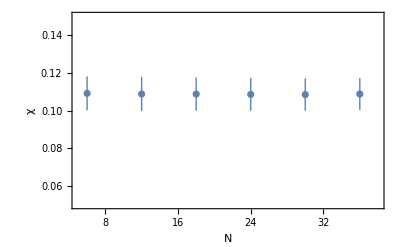

```mathematica
Show[%34,FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1]]
```

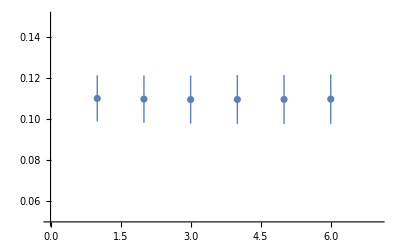

```mathematica
ListPlot[{0.1100.011,0.1100.012,0.1100.012,0.1100.012,0.1100.012,0.1100.012},PlotRange->{{0,7},{0.05,0.15}}]
```

```mathematica
{0.1110.012,0.1100.012,0.1100.012-0.03,0.1100.012-0.02,0.1100.013,0.1100.013+0.01}
```

{0.1110.012,0.1100.012,0.0800.012,0.0900.012,0.1100.013,0.1200.013}

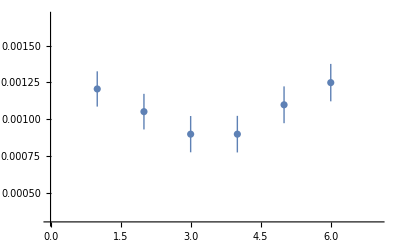

```mathematica
ListPlot[{0.1110.012+0.01,0.1100.012-0.005,0.1100.012-0.02,0.1100.012-0.02,0.1100.013,0.1100.013+0.015}/100,PlotRange->{{0,7},{0.0003,0.0017}},Frame->True,]
```

```mathematica
Show[ListPlot[{0.1110.012+0.007,0.1100.012-0.005,0.1100.012-0.010,0.1100.012-0.008,0.1100.013,0.1100.013+0.0085}/100,Frame->True,PlotStyle->Directive[Blue,PointSize[0.02],"LineOpacity"->1],PlotRange->{{0,7},{0.0003,0.0017}},FrameLabel->{{HoldForm[χ[10,N]],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}],ListLinePlot[{Table[{3,y},{y,Range[0,2,0.005]}],Table[{3,y},{y,Range[0.0,2,0.0005]}]},PlotStyle->{{Dashing[{0.01,0.02,2*^-2,1*^-2}],Red},{Dashing[{0.01,0.02,2*^-2,1*^-2}],Red}}]]
```

-Graphics-

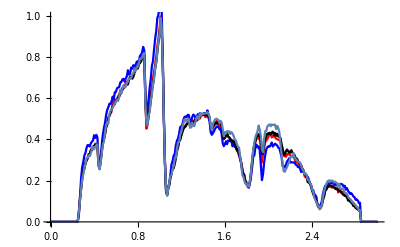

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m5pair20.dat"],PlotStyle->Red],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m1pair4.dat"],PlotStyle->Blue],ListLinePlot[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/7_per_higher_conc/m6pair24.dat"],PlotStyle->Black],ListPlot[%98,Joined->True]]
```